```mathematica
SetDirectory[NotebookDirectory[]<>"plate reader"]
```

/Users/giometto/Desktop/SynologyDrive/Andrea/killer_plate_reader/github/plate reader

```mathematica
dataFiles={"240726_killer_24h.xlsx","240726_killer_48h.xlsx","240726_killer_72h.xlsx","240726_killer_96h.xlsx","240726_killer_120h.xlsx","240726_killer_144h.xlsx","240726_killer_168h.xlsx","240726_killer_192h.xlsx","240726_killer_216h.xlsx","240726_killer_240h.xlsx","240726_killer_264h.xlsx","240726_killer_288h.xlsx"};
```

```mathematica
cols=Import[dataFiles⟦1⟧]⟦1⟧⟦39⟧;
```

```mathematica
data=Import/@dataFiles;
```

```mathematica
end=111;
```

```mathematica
times=Table[1/3i,{i,end-40+1}]/24;
```

```mathematica
bkgod=0.082;
```

### 24 h

```mathematica
(* Treatments order: yAG171 in isolation, yAG177 in isolation, 32 initial fraction K, 36 initial fraction K, 40 initial fraction K, 44 initial fraction K, 48 initial fraction K, 52 initial fraction K *)
```

```mathematica
reps24={{"B3","D7","F11"},{"B2","D6","F10"},{"B4","B10","D8","F4"},{"B6","D2","D10","F6"},{"B5","B11","D9","F5"},{"B8","D4","F2","F8"},{"B9","D5","F3","F9"}};
```

```mathematica
(* Replace first three data points as NaNs because of condensation *)
od600=Table[Table[Table[Flatten[{"NaN","NaN","NaN",Table[data⟦day⟧⟦1⟧⟦k⟧⟦Position[cols,reps24⟦i⟧⟦j⟧]⟦1⟧⟦1⟧⟧,{k,43,end}]}],{j,Length[reps24⟦i⟧]}],{i,Length[reps24]}],{day,1,Length[data]}];
```

```mathematica
avgOD600=Table[Mean[od600⟦day⟧⟦1⟧],{day,1,Length[data]}];
```

### 48 h

```mathematica
(* Treatments order: yAG171 in isolation, yAG177 in isolation, 32 initial fraction K, 36 initial fraction K, 40 initial fraction K, 44 initial fraction K, 48 initial fraction K, 52 initial fraction K *)
```

```mathematica
reps48={{(*"B1",*)"C3",(*"F1",*)"E7","G11"},{"C2",(*"D1",*)"E6","G10"},{"C4","C10","E8","G4"},{"C6","E2","E10","G6"},{"C5","C11","E9","G5"},{"C8","E4","G2","G8"},{"C9","E5","G3","G9"}};
```

```mathematica
(* Replace first three data points as NaNs because of condensation *)
od60048=Table[Table[Table[Flatten[{"NaN","NaN","NaN",Table[data⟦day⟧⟦1⟧⟦k⟧⟦Position[cols,reps48⟦i⟧⟦j⟧]⟦1⟧⟦1⟧⟧,{k,43,end}]}],{j,Length[reps48⟦i⟧]}],{i,Length[reps48]}],{day,1,Length[data]}];
```

```mathematica
avgOD60048=Table[Mean[od60048⟦day⟧⟦1⟧],{day,1,Length[data]}];
```

```mathematica
dataCal=Import["Calibration_data.xlsx"]⟦1⟧;
```

```mathematica
stop=6;
yAG171bOD0=Table[dataCal⟦44⟧⟦3+i⟧,{i,0,stop}]-bkgod
yAG177OD0=Table[dataCal⟦41⟧⟦3+i⟧,{i,0,stop}]-bkgod
```

{1.557,0.735,0.255,0.075,0.018,0.006,0.002}

{1.576,0.674,0.272,0.067,0.017,0.006,0.003}

```mathematica
(* Density of third serial dilution measured at haemocytometer *)
D1density=5.775*10^6;
D2density=6.575*10^6;
(* Calculate original density of undiluted sample *)
oDensityAG171b=(260/80)^3D1density
oDensityAG177=(260/80)^3D2density
```

1.98245×10^8

2.25707×10^8

```mathematica
ODvsNAG171b0=Transpose[{yAG171bOD0,Table[oDensityAG171b(80/260)^i,{i,0,stop}]}]
ODvsNAG1770=Transpose[{yAG177OD0,Table[oDensityAG177(80/260)^i,{i,0,stop}]}]
```

{{1.557,1.98245×10^8},{0.735,6.09984×10^7},{0.255,1.87688×10^7},{0.075,5.775×10^6},{0.018,1.77692×10^6},{0.006,546746.},{0.002,168229.}}

{{1.576,2.25707×10^8},{0.674,6.94484×10^7},{0.272,2.13688×10^7},{0.067,6.575×10^6},{0.017,2.02308×10^6},{0.006,622485.},{0.003,191534.}}

```mathematica
nlm171b=NonlinearModelFit[ODvsNAG171b0,a*x+b*x^2+c x^3,{a,b,c},x(*,Weights->1/Table[oDensityAG171b (50/200)^i,{i,0,stop-1}]*)]
nlm177=NonlinearModelFit[ODvsNAG1770,a*x+b*x^2+c x^3,{a,b,c},x(*,Weights->1/Table[oDensityAG177 (50/200)^i,{i,0,stop-1}]*)]
nlm=NonlinearModelFit[Flatten[{ODvsNAG1770,ODvsNAG171b0},1],a*x+b*x^2+c x^3,{a,b,c},x(*,Weights->1/Table[oDensityAG177 (50/200)^i,{i,0,stop-1}]*)]
```

FittedModel[7.4715×10^7 x-8.97385×10^6 x^2+2.74656×10^7 x^3]

FittedModel[6.68017×10^7 x+5.70036×10^7 x^2-5.40221×10^6 x^3]

FittedModel[8.50307×10^7 x-1.21998×10^7 x^2+2.83394×10^7 x^3]

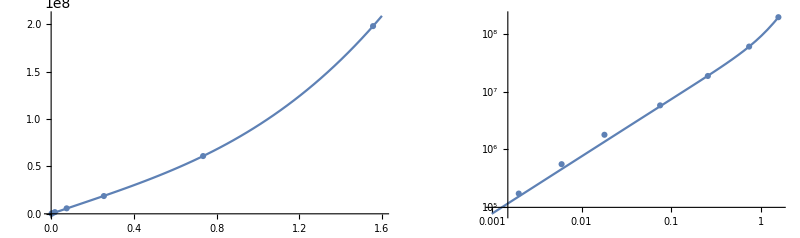

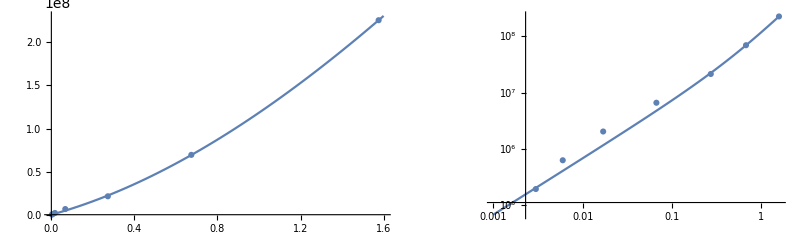

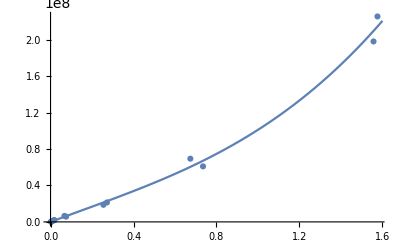

```mathematica
GraphicsRow[{Show[ListPlot[ODvsNAG171b0,PlotMarkers->Automatic,PlotRange->All],Plot[nlm171b[x],{x,0,1.6}],PlotRange->All],
Show[ListLogLogPlot[ODvsNAG171b0,PlotMarkers->Automatic,PlotRange->All],LogLogPlot[nlm171b[x],{x,0.001,1.6}],PlotRange->All]}]
GraphicsRow[{Show[ListPlot[ODvsNAG1770,PlotMarkers->Automatic,PlotRange->All],Plot[nlm177[x],{x,0,1.6}],PlotRange->All],
Show[ListLogLogPlot[ODvsNAG1770,PlotMarkers->Automatic,PlotRange->All],LogLogPlot[nlm177[x],{x,0.001,1.6}],PlotRange->All]}]
Show[ListPlot[Flatten[{ODvsNAG1770,ODvsNAG171b0},1],PlotMarkers->Automatic,PlotRange->All],Plot[nlm[x],{x,0,1.6}]]
```

```mathematica
(* Theoretical limits *)
limitK=1/(1/225+(1-1/225)/(1-Exp[-(0.26/0.28*23.2*0.28+Log[1/225])]))*1.86*10^8
limitS=1/(1/225+(1-1/225)/(1-Exp[-(23.2*0.28+Log[1/225])]))*1.7*10^8
```

8.5737×10^7

1.12433×10^8

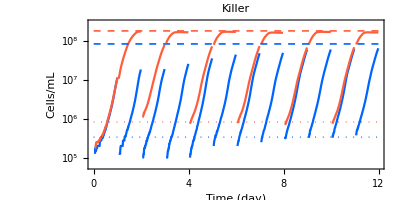

```mathematica
pl1=Show[ListLogPlot[{Flatten[Table[Transpose[{(times+(day-1)),nlm171b/@(Mean[Table[od600⟦day⟧⟦1⟧⟦k⟧-bkgod,{k,1,Length[reps24⟦1⟧]}]])}],{day,Length[data]}],1],Flatten[Table[Transpose[{(times+(day-1)),nlm171b/@(Mean[Table[od60048⟦day⟧⟦1⟧⟦k⟧-bkgod,{k,1,Length[reps48⟦1⟧]}]])}],{day,Length[data]}],1]},Frame->True,FrameLabel->{"Time (day)","Cells/mL"},Joined->True,AspectRatio->1/2,PlotStyle->{RGBColor[0,0.396,1],RGBColor[1,0.369,0.231]},PlotLabel->"Killer",BaseStyle->{Black,FontSize->16},PlotRange->{6 10^4,3 10^8},FrameTicks->{{Automatic,None},{{0,2,4,6,8,10,12},None}}],LogPlot[{limitK,limitK/255,1.86*10^8/225,1.86*10^8},{x,0,12},PlotStyle->{{Dashed,RGBColor[0,0.396,1],Thickness[0.003]},{Dotted,RGBColor[0,0.396,1],Thickness[0.003]},{Dotted,RGBColor[1,0.369,0.231],Thickness[0.003]},{Dashed,RGBColor[1,0.369,0.231],Thickness[0.003]}}],FrameStyle->Black]
```

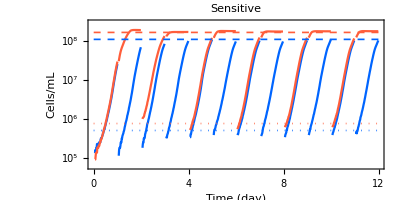

```mathematica
pl2=Show[ListLogPlot[{Flatten[Table[Transpose[{(times+(day-1)),nlm177/@(Mean[Table[od600⟦day⟧⟦2⟧⟦k⟧-bkgod,{k,1,Length[reps24⟦2⟧]}]])}],{day,Length[data]}],1],Flatten[Table[Transpose[{(times+(day-1)),nlm177/@(Mean[Table[od60048⟦day⟧⟦2⟧⟦k⟧-bkgod,{k,1,Length[reps48⟦2⟧]}]])}],{day,Length[data]}],1]},Frame->True,FrameLabel->{"Time (day)","Cells/mL"},Joined->True,AspectRatio->1/2,PlotStyle->{RGBColor[0,0.396,1],RGBColor[1,0.369,0.231]},PlotLabel->"Sensitive",BaseStyle->{Black,FontSize->16},PlotRange->{6 10^4,3 10^8},FrameTicks->{{Automatic,None},{{0,2,4,6,8,10,12},None}}],LogPlot[{limitS,limitS/225,1.7*10^8/225,1.7*10^8},{x,0,12},PlotStyle->{{Dashed,RGBColor[0,0.396,1],Thickness[0.003]},{Dotted,RGBColor[0,0.396,1],Thickness[0.003]},{Dotted,RGBColor[1,0.369,0.231],Thickness[0.003]},{Dashed,RGBColor[1,0.369,0.231],Thickness[0.003]}}],FrameStyle->Black]
```

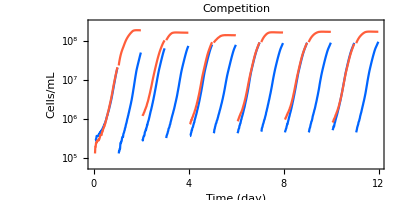

```mathematica
pl3=ListLogPlot[{Flatten[Table[Transpose[{(times+(day-1)),nlm/@(Mean[Table[od600⟦day⟧⟦6⟧⟦k⟧-bkgod,{k,1,Length[reps24⟦6⟧]}]])}],{day,Length[data]}],1],Flatten[Table[Transpose[{(times+(day-1)),nlm/@(Mean[Table[od60048⟦day⟧⟦6⟧⟦k⟧-bkgod,{k,1,Length[reps48⟦6⟧]}]])}],{day,Length[data]}],1]},Frame->True,FrameLabel->{"Time (day)","Cells/mL"},Joined->True,AspectRatio->1/2,PlotStyle->{RGBColor[0,0.396,1],RGBColor[1,0.369,0.231]},PlotLabel->"Competition",BaseStyle->{Black,FontSize->16},FrameStyle->Black,PlotRange->{6 10^4,3 10^8},FrameTicks->{{Automatic,None},{{0,2,4,6,8,10,12},None}}]
```

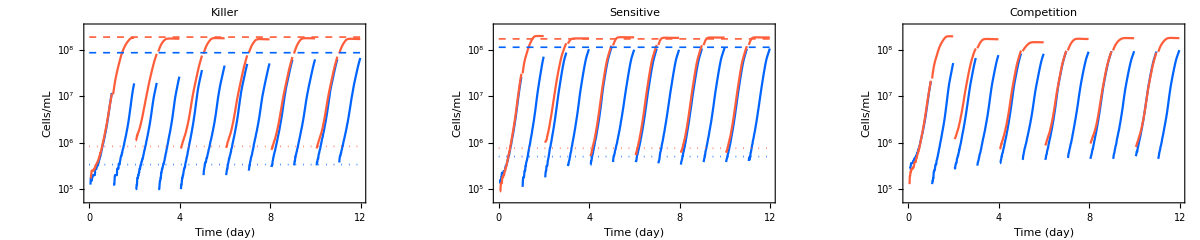

```mathematica
GraphicsRow[{pl1,pl2,pl3},ImageSize->1200]
```